# Development of compression algorithm design (exhaustive search for rule and index and dimensionality)

```mathematica
r = 30 (*The ECA rule number*);
n = 4 (*Data dimensionality*);
p = Tuples[{1,0},n] ;(*All possible permutations*)
```

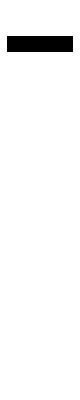
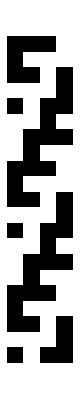
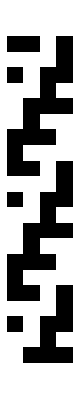
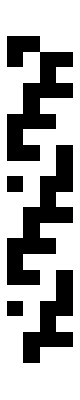
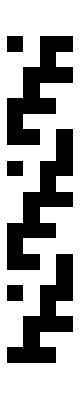
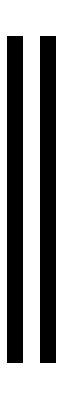
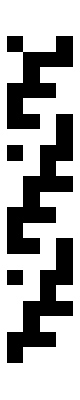
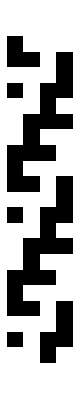
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*evolutions = CellularAutomaton[rule,#,n - Log2[n]]&/@p (*-log2(n) because position must be specified*)*)
evolutions = CellularAutomaton[rule,#,n*5 ]&/@p ;
ArrayPlot/@evolutions
```

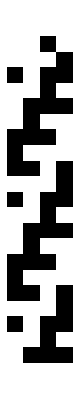
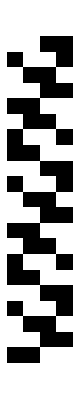
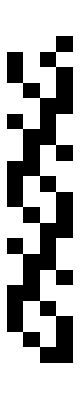
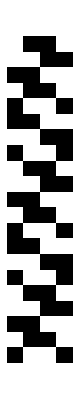
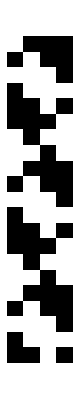
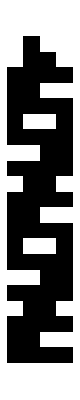
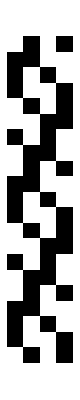
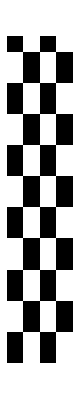
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

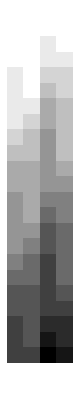
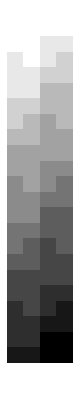
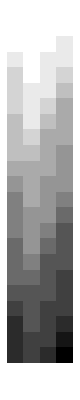
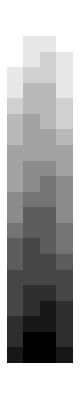
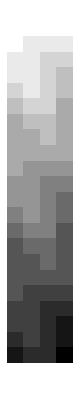
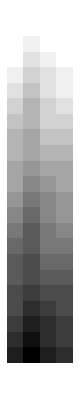
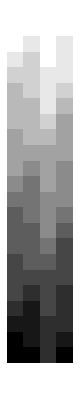
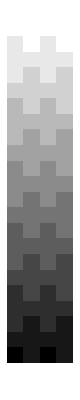

```mathematica
perm = 3; (*One of the permutations that will be compared with all other permutations*)
splitup = TakeDrop[evolutions,{perm}]; (*Remove the permutation we are looking at from the list*)
permevol = Last@splitup;
testperm = First@splitup;
a =Abs[permevol-ConstantArray[First@testperm,Length@permevol]]; (*Identify if the permutation evolution is different from others (if you see zeros, it is the same)*)
ArrayPlot/@a
accum = Accumulate/@a; (*Determine after how many updates the permutation becomes uniquely different (not just zeros)*)
ArrayPlot/@accum
p =Product[accum[[i]],{i,1,Length[accum]}]/.n_Integer/;n>1->1; (*After how many updates is sequence uniqe for all permutations*)
ArrayPlot[p]
```

```mathematica
getShortestUpdate[evolutions_,permutationnumber_]:=(
splitup = TakeDrop[evolutions,{permutationnumber}]; (*Remove the permutation we are looking at from the list*)
permevol = Last@splitup;
testperm = First@splitup;
a =Abs[permevol-ConstantArray[First@testperm,Length@permevol]]; (*Identify if the permutation evolution is different from others*)
accum = Accumulate/@a; (*Determine after how many updates the permutation becomes uniquely different*)
p =Product[accum[[i]],{i,1,Length[accum]}]/.n_Integer/;n>1->1 (*When is the permutation unique for all*)
)

ArrayPlot[getShortestUpdate[evolutions,3]]
```

-Graphics-

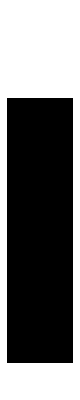
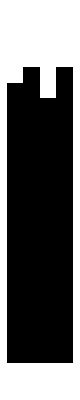
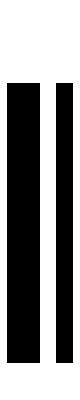
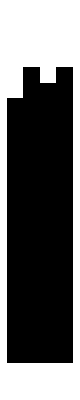
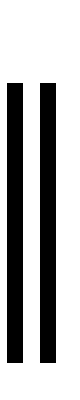
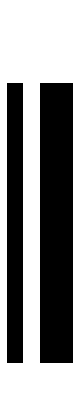
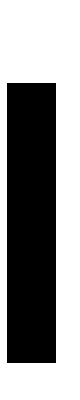
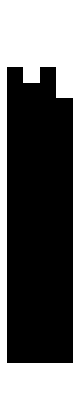
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
allperm =getShortestUpdate[evolutions,#]&/@Range[2^n]; (*Find the shortest update sequence for all permuatations*)
ArrayPlot/@allperm(*White column means cannot be uniqely defined with that read index*)
(*For each permutation have to look at best case*)
```

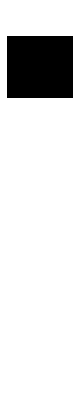
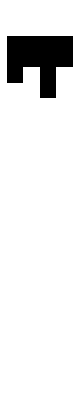
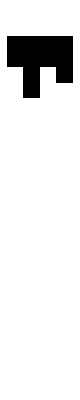
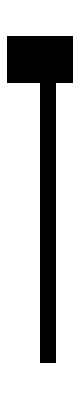
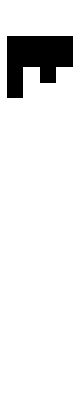
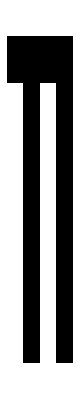
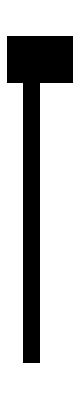
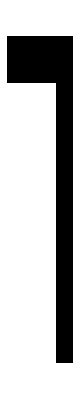
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot/@Abs[allperm-1] (*Basically inverting the colors, Also allows for addition so number of updates required can be calculated*)
```

```mathematica
Total[Abs[allperm-1],{2}] + 1 (*Number of updates required for each permutations at a given index to uniquely define, plus 1 is because only afther the color changes vertically, the data is uniqely defined*)
```

```mathematica
{{5,5,5,5},{4,3,5,3},{3,5,3,4},{4,4,22,4},{5,3,4,3},{4,22,4,22},{4,22,4,4},{4,4,4,22},{3,4,3,5},{4,4,4,22},{22,4,22,4},{22,4,4,4},{22,4,4,4},{4,22,4,4},{4,4,22,4},{22,22,22,22}}
(*In this case when working is n=4 we see that the smallest number we get is 3 which is not small enough since we will need an additional stop bit to indicate whether compression did take place*)
```

```mathematica
mindef = Min/@Total[Abs[allperm-1],{2}] +1 (*Min number of updates to uniqe define for each permutation of the position of the update is specified which would take an additional log2(n) bits to convey*)
```

{5,3,3,4,3,4,4,4,3,4,4,4,4,4,4,22}

```mathematica
mincomrpess = Max[mindef] (*This should be smaller than n-log2(n) if we want to compress to a fixed length every time and specify the read index*)
```

22

```mathematica
(*For rule and dimension*)
```

```mathematica
testRuleAndDim[r_,n_]:=(
p = Tuples[{1,0},n] ;
evolutions = CellularAutomaton[r,#,n*1 ]&/@p ;
(*evolutions = evolutions[[2;;,;;]]; (*This is for first doing update then starting to send bits*)*)
allpermeval =getShortestUpdate[evolutions,#]&/@Range[2^n];
Total[Abs[allpermeval-1],{2}] + 1 
(*Max[Min/@Total[Abs[allpermeval-1],{2}]]*)
(*Mean[Min/@Total[Abs[allpermeval-1],{2}]]*)
(*Min/@Total[Abs[allpermeval-1],{2}]*)
)
```

For dimensionality n = 4 we require the compression to go to 2 bits sent because an additional bit is required for saying if the compression actually happened.

```mathematica
n4 = ParallelTable[testRuleAndDim[i,4],{i,Range[2^4-1]}]//N
Dimensions[n4]
Print["That the minimum update cost is nog small enough (2). It is ",Min[n4]," For dimensionality 4"]
```

{{{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.}},{{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,4.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{4.,6.,6.,6.},{6.,4.,6.,6.},{6.,6.,6.,6.},{6.,6.,4.,6.},{6.,6.,6.,6.},{6.,6.,4.,6.},{6.,6.,6.,4.},{6.,6.,6.,4.},{4.,6.,6.,6.},{6.,6.,6.,6.}},{{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,5.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{5.,6.,6.,6.},{6.,5.,6.,6.},{6.,6.,6.,6.},{6.,6.,5.,6.},{6.,6.,6.,6.},{6.,6.,5.,6.},{6.,6.,6.,5.},{6.,6.,6.,5.},{5.,6.,6.,6.},{6.,6.,6.,6.}},{{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.}},{{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,3.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,3.},{6.,6.,6.,6.},{3.,6.,6.,6.},{6.,3.,6.,6.},{3.,3.,3.,3.}},{{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{5.,4.,4.,3.},{6.,6.,6.,6.},{3.,6.,3.,6.},{4.,4.,3.,5.},{3.,4.,4.,3.},{6.,6.,6.,6.},{3.,5.,4.,4.},{6.,3.,6.,3.},{3.,3.,4.,4.},{4.,3.,5.,4.},{4.,3.,3.,4.},{4.,4.,3.,3.},{6.,6.,6.,6.}},{{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{3.,6.,6.,3.},{6.,6.,6.,6.},{3.,4.,3.,4.},{6.,6.,3.,3.},{3.,4.,6.,6.},{6.,6.,6.,6.},{3.,3.,6.,6.},{4.,3.,4.,3.},{6.,3.,4.,6.},{6.,3.,3.,6.},{6.,6.,3.,4.},{4.,6.,6.,3.},{6.,6.,6.,6.}},{{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.}},{{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.}},{{6.,6.,6.,6.},{5.,6.,5.,6.},{6.,5.,6.,5.},{5.,5.,4.,3.},{5.,6.,5.,6.},{6.,6.,6.,6.},{5.,4.,3.,5.},{6.,4.,6.,3.},{6.,5.,6.,5.},{3.,5.,5.,4.},{6.,6.,6.,6.},{3.,6.,4.,6.},{4.,3.,5.,5.},{6.,3.,6.,4.},{4.,6.,3.,6.},{6.,6.,6.,6.}},{{6.,6.,6.,6.},{6.,6.,4.,5.},{6.,4.,5.,6.},{6.,6.,6.,6.},{4.,5.,6.,6.},{6.,5.,6.,5.},{6.,6.,6.,6.},{6.,6.,6.,4.},{5.,6.,6.,4.},{6.,6.,6.,6.},{5.,6.,5.,6.},{4.,6.,6.,6.},{6.,6.,6.,6.},{6.,4.,6.,6.},{6.,6.,4.,6.},{4.,4.,4.,4.}},{{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.},{6.,6.,6.,6.}},{{4.,4.,4.,4.},{6.,6.,4.,6.},{6.,4.,6.,6.},{6.,6.,3.,6.},{4.,6.,6.,6.},{6.,6.,6.,6.},{6.,3.,6.,6.},{6.,6.,3.,6.},{6.,6.,6.,4.},{6.,6.,6.,3.},{6.,6.,6.,6.},{6.,6.,6.,3.},{3.,6.,6.,6.},{3.,6.,6.,6.},{6.,3.,6.,6.},{3.,3.,3.,3.}},{{5.,5.,5.,5.},{4.,5.,6.,6.},{5.,6.,6.,4.},{6.,6.,6.,6.},{6.,6.,4.,5.},{4.,6.,4.,6.},{6.,6.,6.,6.},{6.,4.,6.,6.},{6.,4.,5.,6.},{6.,6.,6.,6.},{6.,4.,6.,4.},{6.,6.,4.,6.},{6.,6.,6.,6.},{6.,6.,6.,4.},{4.,6.,6.,6.},{6.,6.,6.,6.}},{{4.,4.,4.,4.},{4.,4.,4.,4.},{4.,4.,4.,4.},{4.,4.,4.,4.},{4.,4.,4.,4.},{4.,4.,4.,4.},{4.,4.,4.,4.},{4.,4.,4.,4.},{4.,4.,4.,4.},{4.,4.,4.,4.},{4.,4.,4.,4.},{4.,4.,4.,4.},{4.,4.,4.,4.},{4.,4.,4.,4.},{4.,4.,4.,4.},{4.,4.,4.,4.}}}

{15,16,4}

That the minimum update cost is nog small enough (2). It is 3. For dimensionality 4

Question now becomes, for a given rule and index, what is the most permutations that is below (n-1 -1). For n=4 there is none

Lets consider n=5

{255,32,5}

3.

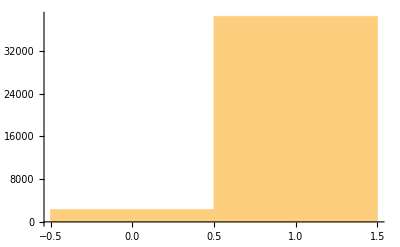

22

{{156,1},{156,2},{156,3},{156,4},{156,5},{198,1},{198,2},{198,3},{198,4},{198,5}}

```mathematica
n5 = ParallelTable[testRuleAndDim[i,5],{i,Range[2^8-1]}]//N;
Dimensions[n5]
Min[n5]
candidates = Unitize[Threshold[n5,4]] ;(*Make everything smaller than 4 equal to zero, then everything larger than zero, 1*)
Histogram[Flatten[candidates]]
Min[Total[candidates,{2}]] 
Position[Total[candidates,{2}],Min[Total[candidates,{2}]]] (*Sum accros the permutation dimenstion*)
```

```mathematica
findBestRuleAndPositionForDim[n_]:=(
updatesrequired = ParallelTable[testRuleAndDim[i,n],{i,Range[2^8-1]}]//N; (*Find number of updates for each rule and each index and each permutation required to uniquely define data*)
bitreduction= 1;
compressindicator = 1;
compressioncandidates = Unitize[Threshold[updatesrequired,n-bitreduction - compressindicator]] ; (*Threshold does smaller or equal to*)(*All indexes at given rule for given permutation that leads to compression of one/two bit is set to zero*)
sumovercandidates = Total[compressioncandidates,{2}]; (*Score of how well a rule and index combination is doing. Lower is better*)
bestnumberofcompressiblepermutations = Min[sumovercandidates];
{1 - bestnumberofcompressiblepermutations/2^n,   (*Fraction compressable*)
Position[sumovercandidates,bestnumberofcompressiblepermutations] }
)
```

```mathematica
findBestRuleAndPositionForDim[9]//N
```

{0.0390625,{{184.,1.},{184.,2.},{184.,3.},{184.,4.},{184.,5.},{184.,6.},{184.,7.},{184.,8.},{184.,9.},{226.,1.},{226.,2.},{226.,3.},{226.,4.},{226.,5.},{226.,6.},{226.,7.},{226.,8.},{226.,9.}}}

```mathematica
|
```

Looks like for dimensionality n=6, we can apply rule 15 and inspect index 1. After 5 updates we should uniquely id the data

Also for n=7 we can apply rule 15, inspect index1 after 5 updates we should be fine?

```mathematica
2^8
```

256

```mathematica
225/256//N
```

0.878906

Suppose that we can specify the rule as one of two for instance.

```mathematica
findBestRulesAndPositionsForDim::usage = "If you can specify rule (2) or position"
findBestRulesAndPositionsForDim[n_]:=(
updatesrequired = ParallelTable[testRuleAndDim[i,n],{i,Range[2^8-1]}]//N; (*Find number of updates for each rule and each index and each permutation required to uniquely define data*)
bitreduction= 1;
compressindicator = 1;
compressioncandidates = Unitize[Threshold[updatesrequired,n-bitreduction - compressindicator]] ; (*Threshold does smaller or equal to*)(*All indexes at given rule for given permutation that leads to compression of one/two bit is set to zero*)
sumovercandidates = Total[compressioncandidates,{2}]; (*Score of how well a rule and index combination is doing. Lower is better*)
bestnumberofcompressiblepermutations = Min[sumovercandidates];
{1 - bestnumberofcompressiblepermutations/2^n,   (*Fraction compressable*)
Position[sumovercandidates,bestnumberofcompressiblepermutations] }
)
```

```mathematica
updatesrequired = ParallelTable[testRuleAndDim[i,6],{i,Range[2^8-1]}]//N;
```

```mathematica
Dimensions[updatesrequired]
```

{255,64,6}

when considering index 1

```mathematica
lookatid1 = updatesrequired[[;;,;;,2]];
Dimensions[lookatid1]
```

{255,64}

```mathematica
Count[#,4.]&/@lookatid1
```

{0,0,0,0,0,1,2,0,0,0,0,0,2,0,0,0,0,0,0,1,2,2,4,0,0,3,1,0,0,0,2,1,0,0,0,0,4,0,1,2,1,0,0,3,0,0,0,0,0,2,0,0,1,2,0,0,0,3,0,0,0,3,0,0,0,0,0,0,2,0,0,0,1,1,0,0,4,1,2,0,0,3,1,0,0,0,2,1,0,0,4,1,2,0,0,2,1,0,0,3,0,0,0,0,0,0,1,0,1,0,0,0,0,3,0,0,0,3,0,0,1,5,0,0,0,4,0,2,4,2,3,0,0,3,0,0,0,0,0,0,1,0,0,2,3,2,2,3,0,0,2,0,0,0,0,0,0,3,1,2,5,2,3,0,0,0,3,0,0,0,0,0,1,0,0,2,3,4,2,0,3,2,0,2,0,2,0,0,0,2,0,0,0,0,0,0,1,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,3,1,0,3,0,0,0,0,0,0,0,0,2,0,0,1,0,0,4,0,0,2,0,0,0,0,0,0,2,0,0,0,2,0,0,2,2,1,0,0,2,0}

```mathematica
ReverseSortBy[lookatid1,Count[#,3.]&]//Column
```

1
 |  |  |  |

```mathematica
updatesrequired = ParallelTable[testRuleAndDim[i,9],{i,Range[2^8-1]}]//N;
```

```mathematica
lookatid1 = updatesrequired[[;;,;;,4]];
ArrayPlot[Unitize[ReverseSortBy[lookatid1,Count[#,4.]&]-4]]
```

-Graphics-

```mathematica
2^6
```

64